## VECTOR CALCULUS

## Preamble

```mathematica
AppendTo[$Path,"C:\\Users\\User\\git\\steptest1\\mma-nbks"];
<<Geometry`
```

## Test-Preamble

```mathematica
(* AppendTo[$Path,"C:\\Users\\Nilo\\__DATA\\Mega\\DATA\\eclipse-workspace\\Geometry"];
<<Geometry` *)
```

```mathematica
AppendTo[$Path,"C:\\Users\\deroo\\__DATA\\MEGA\\DATA\\git\\MFDSNT\\Mathematica Notebooks"];
<<BKPNumberTheory`
<<TestAlgebra` 
<<Geometry`
```

Get::noopen: Cannot open TestAlgebra`.

$Failed

Get::noopen: Cannot open Geometry`.

$Failed

```mathematica
nCollatz[16]
```

{16,8,4,2,1}

## Old-Preamble

```mathematica
(* AppendTo[$Path,"C:\\Users\\Nilo\\__DATA\\Mega\\DATA\\eclipse-workspace\\Geometry"];
<<Geometry` *)
```

```mathematica
AppendTo[$Path,"C:\\Users\\deroo\\__DATA\\MEGA\\DATA\\git\\MFDSNT\\Mathematica Notebooks"];
<<BKPNumberTheory`
<<TestAlgebra` 
<<Geometry`
```

Get::noopen: Cannot open TestAlgebra`.

$Failed

Get::noopen: Cannot open Geometry`.

$Failed

```mathematica
nCollatz[16]
```

{16,8,4,2,1}

## Archived Notes

## Apps

### Case 0

```mathematica
Options[gPolygon]
```

{FaceColor→RGBColor[1, 0, 0],FaceOpacity→1,EdgeColor→GrayLevel[0],EdgeOpacity→1,Thickness→0.0125,Dashing→{2 π,2 π}}

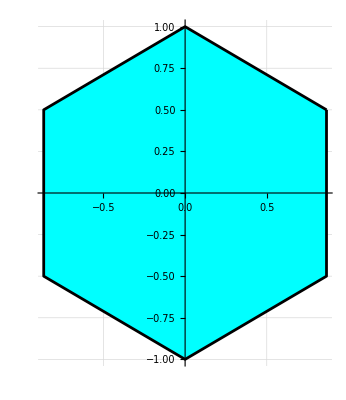

```mathematica
gPolygon[pGon[6],Thickness->0.005,FaceColor->Cyan]//toGL//gr1
```

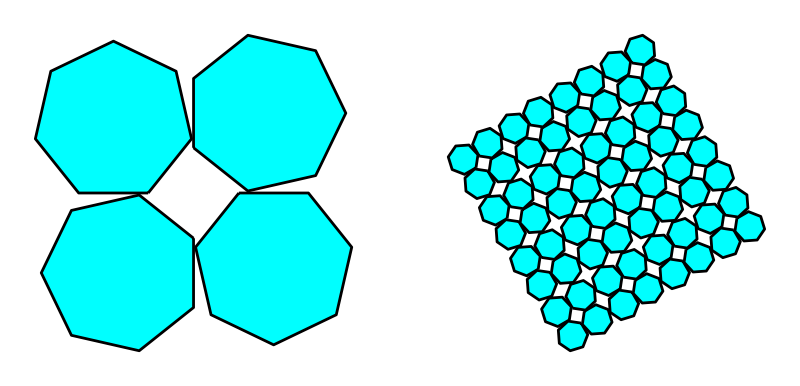

```mathematica
teil[figke_]:= Module[{rotp},
rotp=2mid[figke];
{figke,rot3[figke,{π/2,rotp}],rot3[figke,{π,rotp}],rot3[figke,{3 π /2,rotp}]}]

dpoly:={{{1,{{0,0},{1,0},{1,1},{.5,4.0},{0,1}}},{White,1}},{Black,1,.005,2 π,2 π}}
dpoly:={tra3[newGeo[3,RGBColor[.55,.55,.25,.5]][[1]],{1,1}],{Black,1,.005,2 π,2 π}}

dpoly:=tra3[gPolygon[pGon[7],Thickness->0.005,FaceColor->Cyan],{1,1}]

GraphicsRow[
{
Graphics[Nest[teil,dpoly,1]//toGL],
Graphics[rot3[Nest[teil,dpoly,3],{30 Degree,{0,0}}]//toGL//gr]
}
]
```

### Case 1

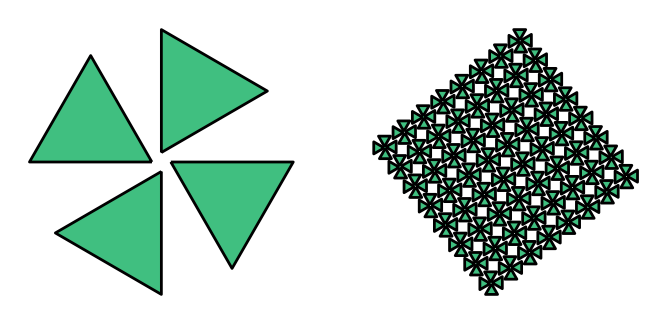

```mathematica
teil[figke_]:= Module[{rotp},
rotp=2mid[figke];
{figke,rot3[figke,{π/2,rotp}],rot3[figke,{π,rotp}],rot3[figke,{3 π /2,rotp}]}]

dpoly:=tra3[newGeo[6],{2,1}]
dpoly:={{{1,{{0,0},{1,0},{1,1},{.5,4.0},{0,1}}},{White,1}},{Black,1,.005,2 π,2 π}}

dpoly:={tra3[newGeo[3,RGBColor[.25,.75,.5,.5]][[1]],{1,1}],{Black,1,.005,2 π,2 π}}
GraphicsRow[{Graphics[Nest[teil,dpoly,1]//toGL],
Graphics[rot3[Nest[teil,dpoly,4],{30 Degree,{0,0}}]//toGL]}]
```

```mathematica
nGonAtEdge3[fig_,{m_,n_}]:=trf3[
trf3[
newGeo[n],
toUnit[toEdges[newGeo[n]][[1,1,1,2]]]//N
],
toVector[toEdges[fig][[m,1,1,2]]]
]
```

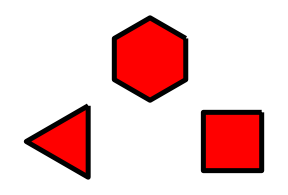

```mathematica
dpoly1:=tra3[newGeo[3],{0,0}]
dpoly2:=tra3[newGeo[4],{4,0}]
dpoly3:=tra3[newGeo[6],{2,2}]
Graphics[{dpoly1,dpoly2,dpoly3}]//toGL
```

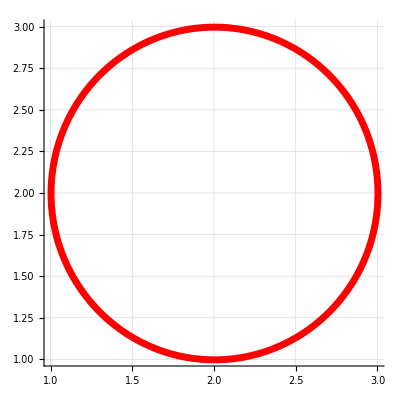

```mathematica
cCircle[{2,2},1]//toGL//gr1
```

### Case 2

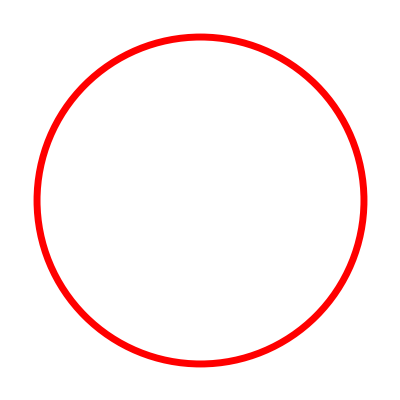

```mathematica
cCircle[{5,5},1.5]//toGL//gr
```

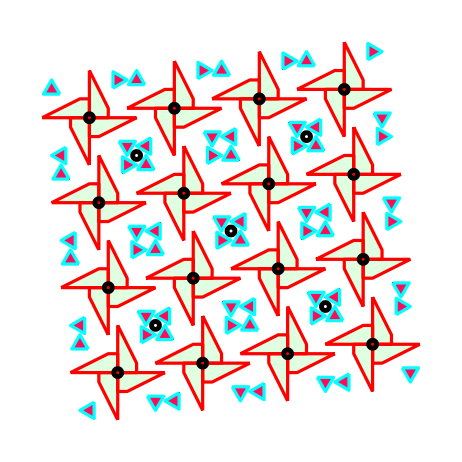

```mathematica
teil[figke_]:= Module[{rotp},
rotp=2mid[figke];
{figke,rot3[figke,{π/2,rotp}],rot3[figke,{π,rotp}],rot3[figke,{3 π /2,rotp}],
repCol[cCircle[rotp,.25],{Black}]
}]

dpolyA:={tra3[newGeo[3,RGBColor[1,.05,.35,.1]][[1]],{1,1}],{Cyan,1,.005,2 π,2 π}}
dpolyB:={{{1,{{4,0},{4,5},{2,5},{2,4}}},{LightGreen,1}},{Red,1,.005,2 π,2 π}}
Nest[teil,{dpolyB,dpolyA},3]//toGL//gr
```

## Tmp-1

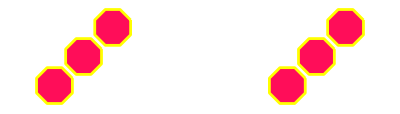

```mathematica
dpolyA:={tra3[newGeo[8,RGBColor[1,.05,.35,.1]][[1]],{1,1}],{Yellow,1,.005,2 π,2 π}}
dpolyA;
dpolyA//toGL;
{dpolyA,tra3[dpolyA,{2,2}]}//toGL ;
{dpolyA,tra3[dpolyA,{1.5,1.5}],tra3[dpolyA,{3.0,3.0}]}//toGL;
{{dpolyA,tra3[dpolyA,{1.5,1.5}],tra3[dpolyA,{3.0,3.0}]},tra3[{dpolyA,tra3[dpolyA,{1.5,1.5}],tra3[dpolyA,{3.0,3.0}]},{12,0}]}//toGL//gr
```

```mathematica
newGeo[1,Red,{{4,4}}]//toGL
```

newGeo[1,RGBColor[1, 0, 0],{{4,4}}]

```mathematica
{RGBColor[1, 0, 0],Opacity[1],{EdgeForm[{GrayLevel[0],Opacity[1],Thickness[0.05],Dashing[{2 π,2 π}]}],Polygon[…]}}//gr
```

-Graphics-

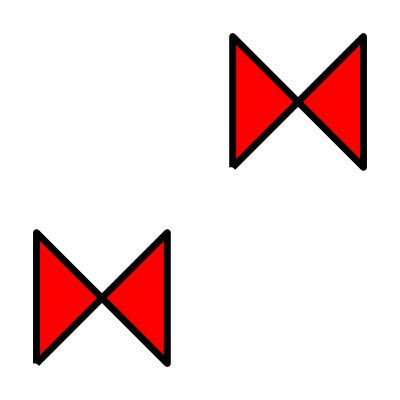

```mathematica
{newGeo[{1,{{0,0},{4,4},{4,0},{0,4}}}],tra3[newGeo[{1,{{0,0},{4,4},{4,0},{0,4}}}],{6,6}]}//toGL//gr
```

```mathematica
CoordinateTransformData[]//tf;
CoordinateChartData[]//tf
```

Bipolar
a | Euclidean | 2
BipolarCylindrical
a | Euclidean | 3
Bispherical
a | Euclidean | 3
Cartesian | Euclidean | 1
Cartesian | Euclidean | 2
Cartesian | Euclidean | 3
Cartesian | Euclidean | 4
Cartesian | Euclidean | 5
Cartesian | Euclidean | 6
Cartesian | Euclidean | 7
Cartesian | Euclidean | 8
Cartesian | Euclidean | 9
Cartesian | Euclidean | 10
CircularParabolic | Euclidean | 3
Confocal | 
α | β | Euclidean | 2
Confocal |  | 
α | β | γ | Euclidean | 3
Confocal |  |  | 
α_1 | α_2 | α_3 | α_4 | Euclidean | 4
Confocal |  |  |  | 
α_1 | α_2 | α_3 | α_4 | α_5 | Euclidean | 5
Confocal |  |  |  |  | 
α_1 | α_2 | α_3 | α_4 | α_5 | α_6 | Euclidean | 6
Confocal |  |  |  |  |  | 
α_1 | α_2 | α_3 | α_4 | α_5 | α_6 | α_7 | Euclidean | 7
Confocal |  |  |  |  |  |  | 
α_1 | α_2 | α_3 | α_4 | α_5 | α_6 | α_7 | α_8 | Euclidean | 8
Confocal |  |  |  |  |  |  |  | 
α_1 | α_2 | α_3 | α_4 | α_5 | α_6 | α_7 | α_8 | α_9 | Euclidean | 9
Confocal |  |  |  |  |  |  |  |  | 
α_1 | α_2 | α_3 | α_4 | α_5 | α_6 | α_7 | α_8 | α_9 | α_10 | Euclidean | 10
Confocal |  |  |  |  |  |  |  |  |  | 
α_1 | α_2 | α_3 | α_4 | α_5 | α_6 | α_7 | α_8 | α_9 | α_10 | α_11 | Euclidean | 11
ConfocalParaboloidal | 
α | β | Euclidean | 3
Conical | 
b | c | Euclidean | 3
Cylindrical | Euclidean | 3
Elliptic
a | Euclidean | 2
EllipticCylindrical
a | Euclidean | 3
Polar | Euclidean | 2
Hyperspherical | Euclidean | 3
Hyperspherical | Euclidean | 4
Hyperspherical | Euclidean | 5
Hyperspherical | Euclidean | 6
Hyperspherical | Euclidean | 7
Hyperspherical | Euclidean | 8
Hyperspherical | Euclidean | 9
Hyperspherical | Euclidean | 10
Hyperspherical | Euclidean | 11
OblateSpheroidal
a | Euclidean | 3
ParabolicCylindrical | Euclidean | 3
PlanarParabolic | Euclidean | 2
ProlateSpheroidal
a | Euclidean | 3
Spherical | Euclidean | 3
Toroidal
a | Euclidean | 3
Standard | Sphere
R | 1
Standard | Sphere
R | 2
Standard | Sphere
R | 3
Standard | Sphere
R | 4
Standard | Sphere
R | 5
Standard | Sphere
R | 6
Standard | Sphere
R | 7
Standard | Sphere
R | 8
Standard | Sphere
R | 9
Standard | Sphere
R | 10
Stereographic | Sphere
R | 1
Stereographic | Sphere
R | 2
Stereographic | Sphere
R | 3
Stereographic | Sphere
R | 4
Stereographic | Sphere
R | 5
Stereographic | Sphere
R | 6
Stereographic | Sphere
R | 7
Stereographic | Sphere
R | 8
Stereographic | Sphere
R | 9
Stereographic | Sphere
R | 10

```mathematica
CoordinateTransform[{"Cartesian"->"Polar",2},{1,-1}]
CoordinateTransform[{"Polar"->"Cartesian",2},{√2,-π/4}]
```

{√2,-π/4}

{1,-1}

```mathematica
FromPolarCoordinates[ToPolarCoordinates[{1/(√2),1/(√2)}]]
FromSphericalCoordinates[ToSphericalCoordinates[{{x,y,z},{1,0,0}}]]
```

{1/(√2),1/(√2)}

{{x,y,z},{1,0,0}}

```mathematica
CoordinateTransform[{"Cartesian"->"Polar",2},{1/√2,-1/√2}]
```

{1,-π/4}

```mathematica
1/((1/√2)+I(1/√2))
```

(1-ⅈ)/(√2)

```mathematica
FromPolarCoordinates[{R,θ}]
ToPolarCoordinates[FromPolarCoordinates[{R,θ}]]
ToPolarCoordinates[FromPolarCoordinates[{R,θ}]]//FullSimplify
```

{R Cos[θ],R Sin[θ]}

{√(R^2 Cos[θ]^2+R^2 Sin[θ]^2),ArcTan[R Cos[θ],R Sin[θ]]}

{√(R^2),ArcTan[R Cos[θ],R Sin[θ]]}

```mathematica
D[Exp[x],x]==Exp[x]
```

True

```mathematica
168-(18+17+15+13+12+15+14)-4
```

60

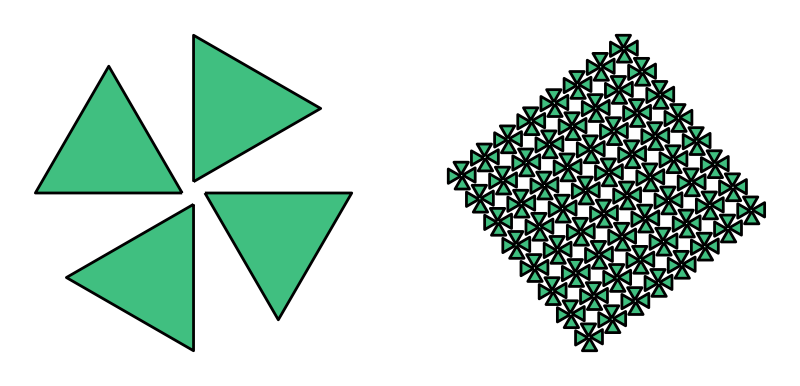

```mathematica
dpoly:={tra3[newGeo[3,RGBColor[.25,.75,.5,.5]][[1]],{1,1}],{Black,1,.005,2 π,2 π}}
GraphicsRow[{Graphics[Nest[teil,dpoly,1]//toGL],
Graphics[rot3[Nest[teil,dpoly,4],{30 Degree,{0,0}}]//toGL]}]
```

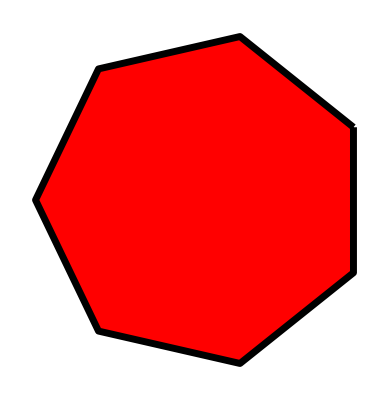

```mathematica
newGeo[7]//toGL//gr
```

```mathematica
nGonAtEdge3[fig_,{m_,n_}]:=trf3[
trf3[
newGeo[n],
toUnit[toEdges[newGeo[n]][[1,1,1,2]]]//N
],
toVector[toEdges[fig][[m,1,1,2]]]
]
```

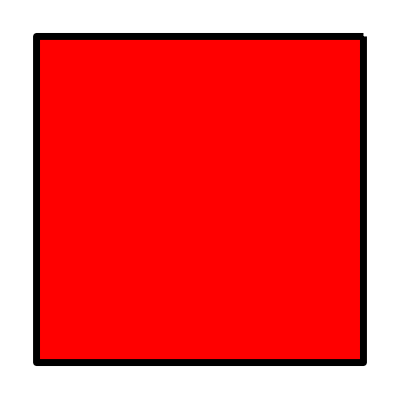

```mathematica
nGonAtEdge3[newGeo[4],{3,4}]//toGL//gr
```

## Tmp-2

```mathematica
Manipulate[
ParametricPlot[{2+2 Cos[a t]+ Cos[b t],2+2 Sin[c t]- Sin[d t]},{t,0,2 Pi},PlotStyle->Thick ],
{a,1,18,1},
{b,1,18,1},
{c,1,18,1},
{d,1,18,1}
]
```

```mathematica
18^4
```

104976

## entity system ??

```mathematica
EntityValue[]
```

{AdministrativeDivision,Aircraft,Airline,Airport,AirportType,Alphabet,AmusementPark,AmusementParkRide,AmusementParkType,AnatomicalConceptIdentifier,AnatomicalFunctionalConcept,AnatomicalSpatialConcept,AnatomicalStructure,AnatomicalTemporalConcept,AnimalAnatomicalStructure,AnimalCoatColorAndPattern,AnimalEggColor,AnimalFeatherColor,AnimalSkinColor,AnimalUse,ArchitecturalStyle,Artwork,AstronomicalObservatory,AstronomicalRadioSource,AtmosphericLayer,AtomicLevel,AtomicLine,BasicFoodGroup,Beach,BioSequenceType,BoardGame,Book,Bridge,BridgeType,BroadcastStation,BroadcastStationClassification,Building,CalculusResult,Canal,Castle,CatBreed,CattleBreed,Cave,Cemetery,Character,Chemical,City,ClimateType,Cloud,CognitiveTask,Color,ColorSet,Comet,Company,ComputationalComplexityClass,Concept,Constellation,ConstructionMaterial,ContinuedFraction,ContinuedFractionResult,ContinuedFractionSource,Country,CrystalFamily,CrystallographicSpaceGroup,CrystalSystem,CurrencyDenomination,CurrencyDenominationType,Dam,DeepSpaceProbe,Desert,Digimon,Dinosaur,Disease,DisplayFormat,DistrictCourt,DogBreed,EarthImpact,Earthquake,EclipseType,ElectricalOutlet,Element,Emotion,EthnicGroup,Exoplanet,FamousChemistryProblem,FamousGem,FamousMathGame,FamousMathProblem,FamousPhysicsProblem,FAOConservationStatus,FictionalCharacter,FictionalPlace,FictionalSpecies,FileFormat,Financial,FiniteGroup,Flight,FlightStatus,Food,FoodAge,FoodAlcoholLabel,FoodBeefGrade,FoodBoneContent,FoodBrandName,FoodCaffeineLabel,FoodCalorieLabel,FoodComposition,FoodConcentration,FoodCrustType,FoodCulture,FoodDataSource,FoodFatLabel,FoodFatType,FoodFiberLabel,FoodFlavor,FoodGeometryType,FoodGlutenContent,FoodIntendedUse,FoodIronLabel,FoodLocation,FoodMaltType,FoodManufacturer,FoodMeatCut,FoodMeatQuality,FoodMoistureLevel,FoodNutritionalSupplement,FoodNutritionalSupplementNotAdded,FoodPackaging,FoodPart,FoodPattyCount,FoodPeelingType,FoodPreparation,FoodProcessingType,FoodSeafoodVariety,FoodSeedContent,FoodServingType,FoodShape,FoodSize,FoodSkinContent,FoodSodiumLabel,FoodState,FoodStorageType,FoodSubBrandName,FoodSugarLabel,FoodSugarType,FoodTexture,FoodTrimmingLevel,FoodType,FoodTypeGroup,FoodVariety,FoodVegetablePart,FoodYeastType,Forest,FrequencyAllocation,FunctionalAnalysisSource,FunctionSpace,Galaxy,Gender,Gene,GeneticTranslationTable,GeographicRegion,GeologicalLayer,GeologicalPeriod,GeometricScene,GivenName,Glacier,GlobalClimateData,GoatBreed,GrammaticalUnit,Graph,HistoricalCountry,HistoricalEvent,HistoricalPeriod,HistoricalSite,HorseBreed,HorseBreedConservationStatus,HorseCoatColorAndPattern,HorseType,HorseUse,ICDNine,ICDTen,Icon,IntegerSequence,InternetDomain,IPAddress,Island,ISO15924Group,Isotope,Knot,Lake,Lamina,Language,LanguageLocale,Laser,Lattice,LatticeSystem,LibraryBranch,LibrarySystem,LightColor,LunarInteriorLayer,MannedSpaceMission,MathematicalFunction,MathWorld,MatterPhase,MeasurementDevice,MedicalTest,MeteorShower,MetropolitanArea,MilitaryConflict,MilitaryConflictType,MilitaryFacilityType,Mine,Mineral,MinorPlanet,MoonPhase,Mountain,Movie,MPAARating,Museum,MusicAct,MusicAlbum,MusicAlbumRelease,MusicAlbumType,MusicalInstrument,MusicWork,MusicWorkRecording,MusicWorkRendition,Mythology,NaturalHazard,NaturalResource,NCBITranslationTableVersion,Nebula,Neighborhood,NetworkService,Neuron,NonperiodicTiling,NotableComputer,NuclearExplosion,NuclearExplosionType,NuclearReactor,NuclearReactorType,NuclearTestSite,Nutrient,ObjectStatus,Ocean,OilField,OperatingStatus,OrganizationType,Park,Particle,ParticleAccelerator,ParticulateMatter,Periodical,PeriodicTiling,Person,PersonTitle,PhysicalActivity,PhysicalConstant,PhysicalEffect,PhysicalQuantity,PhysicalSystem,PigBreed,PigeonBreed,PilatesExercise,PlaneCurve,Planet,PlanetaryMoon,Plant,Pokemon,PokemonAbilities,PokemonGeneration,PokemonPokedexColor,PokemonType,Polyhedron,PopularCurve,PoultryBreed,PoultryBreedConservationStatus,PreservationStatus,PrivateSchool,ProgrammingLanguage,Protein,PublicSchool,Pulsar,Reef,Religion,ReserveLand,RiemannHypothesisFormulation,River,Rocket,RocketFunction,Satellite,SchoolDistrict,SheepBreed,Ship,Shipwreck,SkinType,SNP,SolarSystemFeature,Solid,Sound,Source,SpaceCurve,Species,Sport,SportMatch,SportObject,Stadium,Star,StarCluster,StatisticalGroup,StormType,Supernova,SupernovaType,Surface,Surname,SystemModel,TaxonomicRank,TerrainType,TidalConstituent,TideStation,TimeZone,TopLevelDomain,TopologicalSpaceType,Transparency,TropicalStorm,Tunnel,UnderseaFeature,University,USCongressionalDistrict,USDAEggSize,USDAFoodGroup,VisualArtsArtForm,VisualArtsArtGenre,Volcano,Waterfall,WeatherStation,WeightTrainingExercise,WolframDemonstration,WolframLanguageSymbol,Word,WritingDirection,WritingScript,WritingScriptBaseline,WritingScriptLigature,WritingScriptStatus,WritingScriptType,WritingScriptWhiteSpace,YogaPose,YogaPosition,YogaProp,YogaSequence,ZIPCode}

```mathematica
lst=%;
```

```mathematica
lst
```

{AdministrativeDivision,Aircraft,Airline,Airport,AirportType,Alphabet,AmusementPark,AmusementParkRide,AmusementParkType,AnatomicalConceptIdentifier,AnatomicalFunctionalConcept,AnatomicalSpatialConcept,AnatomicalStructure,AnatomicalTemporalConcept,AnimalAnatomicalStructure,AnimalCoatColorAndPattern,AnimalEggColor,AnimalFeatherColor,AnimalSkinColor,AnimalUse,ArchitecturalStyle,Artwork,AstronomicalObservatory,AstronomicalRadioSource,AtmosphericLayer,AtomicLevel,AtomicLine,BasicFoodGroup,Beach,BioSequenceType,BoardGame,Book,Bridge,BridgeType,BroadcastStation,BroadcastStationClassification,Building,CalculusResult,Canal,Castle,CatBreed,CattleBreed,Cave,Cemetery,Character,Chemical,City,ClimateType,Cloud,CognitiveTask,Color,ColorSet,Comet,Company,ComputationalComplexityClass,Concept,Constellation,ConstructionMaterial,ContinuedFraction,ContinuedFractionResult,ContinuedFractionSource,Country,CrystalFamily,CrystallographicSpaceGroup,CrystalSystem,CurrencyDenomination,CurrencyDenominationType,Dam,DeepSpaceProbe,Desert,Digimon,Dinosaur,Disease,DisplayFormat,DistrictCourt,DogBreed,EarthImpact,Earthquake,EclipseType,ElectricalOutlet,Element,Emotion,EthnicGroup,Exoplanet,FamousChemistryProblem,FamousGem,FamousMathGame,FamousMathProblem,FamousPhysicsProblem,FAOConservationStatus,FictionalCharacter,FictionalPlace,FictionalSpecies,FileFormat,Financial,FiniteGroup,Flight,FlightStatus,Food,FoodAge,FoodAlcoholLabel,FoodBeefGrade,FoodBoneContent,FoodBrandName,FoodCaffeineLabel,FoodCalorieLabel,FoodComposition,FoodConcentration,FoodCrustType,FoodCulture,FoodDataSource,FoodFatLabel,FoodFatType,FoodFiberLabel,FoodFlavor,FoodGeometryType,FoodGlutenContent,FoodIntendedUse,FoodIronLabel,FoodLocation,FoodMaltType,FoodManufacturer,FoodMeatCut,FoodMeatQuality,FoodMoistureLevel,FoodNutritionalSupplement,FoodNutritionalSupplementNotAdded,FoodPackaging,FoodPart,FoodPattyCount,FoodPeelingType,FoodPreparation,FoodProcessingType,FoodSeafoodVariety,FoodSeedContent,FoodServingType,FoodShape,FoodSize,FoodSkinContent,FoodSodiumLabel,FoodState,FoodStorageType,FoodSubBrandName,FoodSugarLabel,FoodSugarType,FoodTexture,FoodTrimmingLevel,FoodType,FoodTypeGroup,FoodVariety,FoodVegetablePart,FoodYeastType,Forest,FrequencyAllocation,FunctionalAnalysisSource,FunctionSpace,Galaxy,Gender,Gene,GeneticTranslationTable,GeographicRegion,GeologicalLayer,GeologicalPeriod,GeometricScene,GivenName,Glacier,GlobalClimateData,GoatBreed,GrammaticalUnit,Graph,HistoricalCountry,HistoricalEvent,HistoricalPeriod,HistoricalSite,HorseBreed,HorseBreedConservationStatus,HorseCoatColorAndPattern,HorseType,HorseUse,ICDNine,ICDTen,Icon,IntegerSequence,InternetDomain,IPAddress,Island,ISO15924Group,Isotope,Knot,Lake,Lamina,Language,LanguageLocale,Laser,Lattice,LatticeSystem,LibraryBranch,LibrarySystem,LightColor,LunarInteriorLayer,MannedSpaceMission,MathematicalFunction,MathWorld,MatterPhase,MeasurementDevice,MedicalTest,MeteorShower,MetropolitanArea,MilitaryConflict,MilitaryConflictType,MilitaryFacilityType,Mine,Mineral,MinorPlanet,MoonPhase,Mountain,Movie,MPAARating,Museum,MusicAct,MusicAlbum,MusicAlbumRelease,MusicAlbumType,MusicalInstrument,MusicWork,MusicWorkRecording,MusicWorkRendition,Mythology,NaturalHazard,NaturalResource,NCBITranslationTableVersion,Nebula,Neighborhood,NetworkService,Neuron,NonperiodicTiling,NotableComputer,NuclearExplosion,NuclearExplosionType,NuclearReactor,NuclearReactorType,NuclearTestSite,Nutrient,ObjectStatus,Ocean,OilField,OperatingStatus,OrganizationType,Park,Particle,ParticleAccelerator,ParticulateMatter,Periodical,PeriodicTiling,Person,PersonTitle,PhysicalActivity,PhysicalConstant,PhysicalEffect,PhysicalQuantity,PhysicalSystem,PigBreed,PigeonBreed,PilatesExercise,PlaneCurve,Planet,PlanetaryMoon,Plant,Pokemon,PokemonAbilities,PokemonGeneration,PokemonPokedexColor,PokemonType,Polyhedron,PopularCurve,PoultryBreed,PoultryBreedConservationStatus,PreservationStatus,PrivateSchool,ProgrammingLanguage,Protein,PublicSchool,Pulsar,Reef,Religion,ReserveLand,RiemannHypothesisFormulation,River,Rocket,RocketFunction,Satellite,SchoolDistrict,SheepBreed,Ship,Shipwreck,SkinType,SNP,SolarSystemFeature,Solid,Sound,Source,SpaceCurve,Species,Sport,SportMatch,SportObject,Stadium,Star,StarCluster,StatisticalGroup,StormType,Supernova,SupernovaType,Surface,Surname,SystemModel,TaxonomicRank,TerrainType,TidalConstituent,TideStation,TimeZone,TopLevelDomain,TopologicalSpaceType,Transparency,TropicalStorm,Tunnel,UnderseaFeature,University,USCongressionalDistrict,USDAEggSize,USDAFoodGroup,VisualArtsArtForm,VisualArtsArtGenre,Volcano,Waterfall,WeatherStation,WeightTrainingExercise,WolframDemonstration,WolframLanguageSymbol,Word,WritingDirection,WritingScript,WritingScriptBaseline,WritingScriptLigature,WritingScriptStatus,WritingScriptType,WritingScriptWhiteSpace,YogaPose,YogaPosition,YogaProp,YogaSequence,ZIPCode}

```mathematica
EntityValue[Entity["PlanetaryMoon","Titan"],"Gravity"]
```

1.3532 m/s^2

```mathematica
EntityValue["MathWorld","Entities"]
(*
EntityValue["PlanetaryMoon","Properties"]
EntityValue["Planet","EntityClasses"]
EntityValue["Planet","PropertyClasses"]
*)
```

```mathematica
lst1=%;
```

```mathematica
lst1//Length
```

13922

```mathematica
lst//tf
```

AdministrativeDivision
Aircraft
Airline
Airport
AirportType
Alphabet
AmusementPark
AmusementParkRide
AmusementParkType
AnatomicalConceptIdentifier
AnatomicalFunctionalConcept
AnatomicalSpatialConcept
AnatomicalStructure
AnatomicalTemporalConcept
AnimalAnatomicalStructure
AnimalCoatColorAndPattern
AnimalEggColor
AnimalFeatherColor
AnimalSkinColor
AnimalUse
ArchitecturalStyle
Artwork
AstronomicalObservatory
AstronomicalRadioSource
AtmosphericLayer
AtomicLevel
AtomicLine
BasicFoodGroup
Beach
BioSequenceType
BoardGame
Book
Bridge
BridgeType
BroadcastStation
BroadcastStationClassification
Building
CalculusResult
Canal
Castle
CatBreed
CattleBreed
Cave
Cemetery
Character
Chemical
City
ClimateType
Cloud
CognitiveTask
Color
ColorSet
Comet
Company
ComputationalComplexityClass
Concept
Constellation
ConstructionMaterial
ContinuedFraction
ContinuedFractionResult
ContinuedFractionSource
Country
CrystalFamily
CrystallographicSpaceGroup
CrystalSystem
CurrencyDenomination
CurrencyDenominationType
Dam
DeepSpaceProbe
Desert
Digimon
Dinosaur
Disease
DisplayFormat
DistrictCourt
DogBreed
EarthImpact
Earthquake
EclipseType
ElectricalOutlet
Element
Emotion
EthnicGroup
Exoplanet
FamousChemistryProblem
FamousGem
FamousMathGame
FamousMathProblem
FamousPhysicsProblem
FAOConservationStatus
FictionalCharacter
FictionalPlace
FictionalSpecies
FileFormat
Financial
FiniteGroup
Flight
FlightStatus
Food
FoodAge
FoodAlcoholLabel
FoodBeefGrade
FoodBoneContent
FoodBrandName
FoodCaffeineLabel
FoodCalorieLabel
FoodComposition
FoodConcentration
FoodCrustType
FoodCulture
FoodDataSource
FoodFatLabel
FoodFatType
FoodFiberLabel
FoodFlavor
FoodGeometryType
FoodGlutenContent
FoodIntendedUse
FoodIronLabel
FoodLocation
FoodMaltType
FoodManufacturer
FoodMeatCut
FoodMeatQuality
FoodMoistureLevel
FoodNutritionalSupplement
FoodNutritionalSupplementNotAdded
FoodPackaging
FoodPart
FoodPattyCount
FoodPeelingType
FoodPreparation
FoodProcessingType
FoodSeafoodVariety
FoodSeedContent
FoodServingType
FoodShape
FoodSize
FoodSkinContent
FoodSodiumLabel
FoodState
FoodStorageType
FoodSubBrandName
FoodSugarLabel
FoodSugarType
FoodTexture
FoodTrimmingLevel
FoodType
FoodTypeGroup
FoodVariety
FoodVegetablePart
FoodYeastType
Forest
FrequencyAllocation
FunctionalAnalysisSource
FunctionSpace
Galaxy
Gender
Gene
GeneticTranslationTable
GeographicRegion
GeologicalLayer
GeologicalPeriod
GeometricScene
GivenName
Glacier
GlobalClimateData
GoatBreed
GrammaticalUnit
Graph
HistoricalCountry
HistoricalEvent
HistoricalPeriod
HistoricalSite
HorseBreed
HorseBreedConservationStatus
HorseCoatColorAndPattern
HorseType
HorseUse
ICDNine
ICDTen
Icon
IntegerSequence
InternetDomain
IPAddress
Island
ISO15924Group
Isotope
Knot
Lake
Lamina
Language
LanguageLocale
Laser
Lattice
LatticeSystem
LibraryBranch
LibrarySystem
LightColor
LunarInteriorLayer
MannedSpaceMission
MathematicalFunction
MathWorld
MatterPhase
MeasurementDevice
MedicalTest
MeteorShower
MetropolitanArea
MilitaryConflict
MilitaryConflictType
MilitaryFacilityType
Mine
Mineral
MinorPlanet
MoonPhase
Mountain
Movie
MPAARating
Museum
MusicAct
MusicAlbum
MusicAlbumRelease
MusicAlbumType
MusicalInstrument
MusicWork
MusicWorkRecording
MusicWorkRendition
Mythology
NaturalHazard
NaturalResource
NCBITranslationTableVersion
Nebula
Neighborhood
NetworkService
Neuron
NonperiodicTiling
NotableComputer
NuclearExplosion
NuclearExplosionType
NuclearReactor
NuclearReactorType
NuclearTestSite
Nutrient
ObjectStatus
Ocean
OilField
OperatingStatus
OrganizationType
Park
Particle
ParticleAccelerator
ParticulateMatter
Periodical
PeriodicTiling
Person
PersonTitle
PhysicalActivity
PhysicalConstant
PhysicalEffect
PhysicalQuantity
PhysicalSystem
PigBreed
PigeonBreed
PilatesExercise
PlaneCurve
Planet
PlanetaryMoon
Plant
Pokemon
PokemonAbilities
PokemonGeneration
PokemonPokedexColor
PokemonType
Polyhedron
PopularCurve
PoultryBreed
PoultryBreedConservationStatus
PreservationStatus
PrivateSchool
ProgrammingLanguage
Protein
PublicSchool
Pulsar
Reef
Religion
ReserveLand
RiemannHypothesisFormulation
River
Rocket
RocketFunction
Satellite
SchoolDistrict
SheepBreed
Ship
Shipwreck
SkinType
SNP
SolarSystemFeature
Solid
Sound
Source
SpaceCurve
Species
Sport
SportMatch
SportObject
Stadium
Star
StarCluster
StatisticalGroup
StormType
Supernova
SupernovaType
Surface
Surname
SystemModel
TaxonomicRank
TerrainType
TidalConstituent
TideStation
TimeZone
TopLevelDomain
TopologicalSpaceType
Transparency
TropicalStorm
Tunnel
UnderseaFeature
University
USCongressionalDistrict
USDAEggSize
USDAFoodGroup
VisualArtsArtForm
VisualArtsArtGenre
Volcano
Waterfall
WeatherStation
WeightTrainingExercise
WolframDemonstration
WolframLanguageSymbol
Word
WritingDirection
WritingScript
WritingScriptBaseline
WritingScriptLigature
WritingScriptStatus
WritingScriptType
WritingScriptWhiteSpace
YogaPose
YogaPosition
YogaProp
YogaSequence
ZIPCode

```mathematica
lst1//tf
```

## Hyperbolic Geometry

## Pre-Amble

### Decomposition Möbius Transformation

```mathematica
Unprotect[C,D];
ClearAll[A,B,C,D,z];
ClearAll[f];
```

```mathematica
A=1+I;
B=I;
C=-I;
D=1-I;

D/C
A/C
(B C - A D)/C^2
```

1+ⅈ

-1+ⅈ

1

```mathematica
f[z_]:=(A z+B)/(C z+D);

f1[z_]:=z+D/C
f2[z_]:=1/z
f3[z_]:=(B C - A D)/C^2 z
f4[z_]:=z+A/C
```

```mathematica
f1[z]//FullSimplify
f2[z]//FullSimplify
f3[z]//FullSimplify
f4[z]//FullSimplify
f4[f3[f2[f1[z]]]]//FullSimplify
f[z]
```

D/C+z

1/z

((B C-A D) z)/C^2

A/C+z

(B+A z)/(D+C z)

(B+A z)/(D+C z)

### Try-Out: HP to Disk ; Disk to HP ; HP to HP ; ?? Disk to Disk (*** NOT WORKING ??? ***)

```mathematica
Unprotect[C,D];
ClearAll[A,B,C,D,z];
ClearAll[f,fA, hTOd,dTOh];
```

```mathematica
A=1;
B=2;
C=3;
D=4;

D/C
A/C
(B C - A D)/C^2
```

4/3

1/3

2/9

```mathematica
f1[z_]:=z+D/C
f2[z_]:=1/z
f3[z_]:=(B C - A D)/C^2 z
f4[z_]:=z+A/C
f[z_]:=(A z+B)/(C z+D);
f1[z]//FullSimplify
f2[z]//FullSimplify
f3[z]//FullSimplify
f4[z]//FullSimplify
f4[f3[f2[f1[z]]]]//FullSimplify
f[z]
```

D/C+z

1/z

((B C-A D) z)/C^2

A/C+z

(B+A z)/(D+C z)

(B+A z)/(D+C z)

#### testcase

```mathematica
A=1;B=2I;C=3I;D=2;
A=1;B=2;C=3;D=4;
hTOd[z_]:=I((1-z)/(1+z))
dTOh[z_]:=InverseFunction[hTOd][z]
fA[z_]:=hTOd[f[dTOh[z]]]
```

```mathematica
fA[z]//FullSimplify
```

-2/(5 ⅈ+z)

```mathematica
fA[0.5I]
```

0.+0.363636 ⅈ

```mathematica
g[z_]:=-2/(z+5I)
```

```mathematica
fA[0.5]

g[0.5]

g[z]
```

-0.039604+0.39604 ⅈ

-0.039604+0.39604 ⅈ

-2/(5 ⅈ+z)

```mathematica
Solve[f[z]==z,z]//FullSimplify;
x1=Solve[f[z]==z,z][[1,1,2]];
x2=Solve[f[z]==z,z][[2,1,2]];
```

```mathematica
x1//FullSimplify
x2//FullSimplify
f[x1]//FullSimplify;
```

1/6 (-3-√33)

1/6 (-3+√33)

## The Upper-half Plane Model (ℍ) of Hyperbolic Geometry

## Tmp-Notes

## Tmp-1

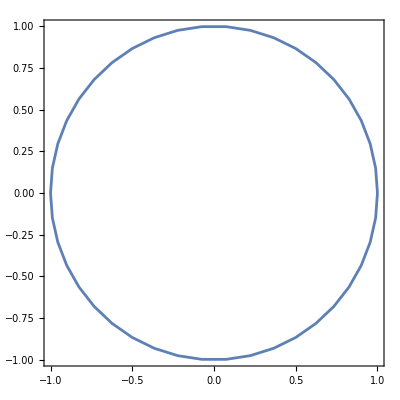

```mathematica
reg1=Region[RegionUnion[Rectangle[{1,1}],Triangle[]]];
reg2=ImplicitRegion[x^2+y^2<=1,{x,y}];
reg3=Region[Circle[]];
RegionPlot[reg3]
```

## Tmp-2

```mathematica
Unprotect[C,D];
ClearAll[A,B,C,D,a1,a2,b,c,d,t,t1,t2,x,y];
a1={{A,B},{C,D}};
a2={{P,Q},{R,S}};
b={0,0};
c={0,0};
d=1;
t1=LinearFractionalTransform[{a1,b,c,d}]
t2=LinearFractionalTransform[{a2,b,c,d}]
t1[{z,1}].Transpose[t2[{z,1}]]
t1[{z,1}][[1]]/t1[{z,1}][[2]]
```

TransformationFunction[(A | B | 0
C | D | 0
0 | 0 | 1)]

TransformationFunction[(P | Q | 0
R | S | 0
0 | 0 | 1)]

(B+A z) (Q+P z)+(D+C z) (S+R z)

(B+A z)/(D+C z)

## Tmp-3

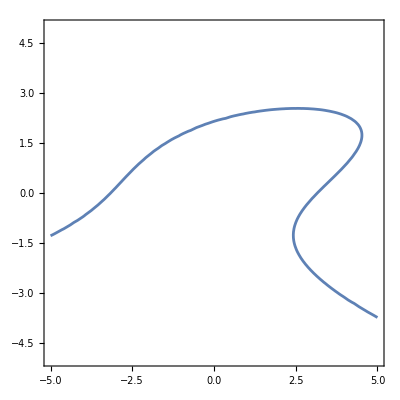

```mathematica
ContourPlot[x^2-2 x y+y^3==10,{x,-5,5},{y,-5,5}]
```

## Tmp-4

```mathematica
p={2,2};
q={6,4};
r={2,3};
s={6,5};
t={6,6};
{
gHLineHP[p,q,Thickness->0.0075,Color->Black],
gHLineHP[r,s,Thickness->0.0075,Color->Black],
gHLineHP[r,t,Thickness->0.0075,Color->Black]
}//toGL//gr1
```

-Graphics-

```mathematica
EuclideanDistance[{11/2,0},{2,2}]//N
EuclideanDistance[{11/2,0},{6,4}]//N
```

4.03113

4.03113

```mathematica
x=-(√2)/2;
y=(√2)/2;
```

```mathematica
ClearAll[f]
f[z_]:=Re[z]/(1-Im[z])
```

```mathematica
f[-1/2+1/2 √3 I]//N
```

-3.73205

## Tmp-5

```mathematica
ClearAll[z]
((z+Conjugate[z])/2)/(1-(z-Conjugate[z])/(2I))//Simplify
((z+Conjugate[z])/2)/(1-(z-Conjugate[z])/(2I))//FullSimplify
```

-(ⅈ (z+Conjugate[z]))/(-2 ⅈ+z-Conjugate[z])

Re[z]/(1-Im[z])

## Tmp-6

```mathematica
u={1,4};
v={2,3};
2 Dot[u,v]
```

28

```mathematica
Conjugate[1+4I](2+3I)+(1+4I)Conjugate[2+3I]
```

28

```mathematica
Abs[1+4I]
Norm[u]
```

√17

√17

```mathematica
Conjugate[1+4I](1+4I)
```

17

```mathematica
add[u_,v_]:=Module[
{x,y},
x=u[[1]]+I u[[2]];
y=v[[1]]+I v[[2]];
(x+y)/(1+Conjugate[x]y)
]
```

```mathematica
add[{0.8,0.4},{-0.2,0.8}]
```

0.83691+0.515021 ⅈ

```mathematica
Norm[4+3I]
Norm[2 √2+2 √2 I]
```

5

4

```mathematica
ToSphericalCoordinates[{1,1,0}]
```

```mathematica
{√2,π/2,π/4}^2
```

{2,π^2/4,π^2/16}

```mathematica
ResourceFunction["StereographicProjection"][{1/2,1/2 √3,0}]
```

{1/2,(√3)/2}

```mathematica
ResourceFunction["InverseStereographicProjection"][{1,5}]
```

{2/27,10/27,25/27}

```mathematica
19^2
```

361

```mathematica
ResourceFunction["StereographicProjection"][{2/27,10/27,25/27}]
```

{1,5}

```mathematica
ResourceFunction["StereographicProjection"][ResourceFunction["InverseStereographicProjection"][{1.6,1.4}]]
```

{1.6,1.4}

```mathematica
ResourceFunction["InverseStereographicProjection"][{1/2,1}]
1/(Abs[1/2+I]^2+1)
2/(Abs[1/2+I]^2+1)
(Abs[1/2+I]^2-1)/(Abs[1/2+I]^2+1)
```

{4/9,8/9,1/9}

4/9

8/9

1/9

```mathematica
Abs[(√2)/2 I+(√2)/2]
Arg[(√2)/2 I+(√2)/2]
ToPolarCoordinates[ReIm[(√2)/2 I+(√2)/2]]
```

1

π/4

{1,π/4}

```mathematica
FromPolarCoordinates[{1,7Pi/12}]
```

{-(-1+√3)/(2 √2),(1+√3)/(2 √2)}

```mathematica
PrimeQ[74207281]
```

True

```mathematica
IntegerName[1000000000000,"Dutch"]
```

een biljoen

```mathematica
ComplexPlot[((z^2-1)(z-2-I)^2)/(z^2+2+2I),{z,-4-4I,4+4I}]
```

-Graphics-

```mathematica
ComplexPlot[((z^2-1)^12)/1,{z,-2-2I,2+2I},Frame->False]
```

-Graphics-

```mathematica
ComplexPlot[Exp[1/z],{z,-0.5-0.5I,0.5+0.5I},Frame->True]
```

-Graphics-

```mathematica
ComplexPlot[z^6,{z,2},Frame->True]
```

-Graphics-

### test-1

```mathematica
(* g looks wrong *)
g[z_]:=-I Log[z+√(z^2)-1]
h[z_]:=π/2+ⅈ Log[ⅈ z+√(1-z^2)]
```

```mathematica
ArcCos[z]//TrigToExp
```

π/2+ⅈ Log[ⅈ z+√(1-z^2)]

```mathematica
Limit[k(z^(1/k)-1),k->Infinity]
```

Log[z]

```mathematica
g[√3/2]==ArcCos[√3/2]
h[√3/2]==ArcCos[√3/2]
ArcCos[√3/2]
```

False

True

π/6

### test-2

```mathematica
(* g corrected *)
g[z_]:=-I Log[z+√(z^2-1)]
h[z_]:=π/2+ⅈ Log[ⅈ z+√(1-z^2)]
ArcCos[z]//TrigToExp
```

π/2+ⅈ Log[ⅈ z+√(1-z^2)]

```mathematica
g[√3/2]==ArcCos[√3/2]
h[√3/2]==ArcCos[√3/2]
ArcCos[√3/2]
```

True

True

π/6

```mathematica
-I Log[z+√(z^2-1)]//FullSimplify
π/2+ⅈ Log[ⅈ z+√(1-z^2)]//FullSimplify
```

-ⅈ Log[z+√(-1+z^2)]

ArcCos[z]

```mathematica
EulerGamma//N
```

0.577216

```mathematica
ClearAll[t]
```

```mathematica
Integrate[1/(√(1-t^2)),{t,z,1}]//TrigToExp
```

ConditionalExpression[π/2+ⅈ Log[ⅈ z+√(1-z^2)], 0<Re[z]<1&&Im[z]==0]

## Tmp-7

```mathematica
√(2 √(2 √(2 √(2 √(2 √2)))))//N
```

1.97846

```mathematica
D[Sin[x^2],{x,1}]
D[Sin[x^2],{x,2}]
```

2 x Cos[x^2]

2 Cos[x^2]-4 x^2 Sin[x^2]

```mathematica
u={1,2,3};
v={2,1,2};
Cross[u,v]
```

{1,2,3}

{2,1,2}

{1,4,-3}

```mathematica
Norm[Cross[u,v]]
```

√26

```mathematica
Norm[u]Norm[v]
```

3 √14

```mathematica
1/0.9
```

1.11111

```mathematica
1/0.021
```

47.619

```mathematica
Sech[3]//N
```

0.0993279

```mathematica
ComplexPlot3D[Sech[z],{z,-7-I π,3+7I π},PlotLegends->Automatic]
```

-Graphics3D-